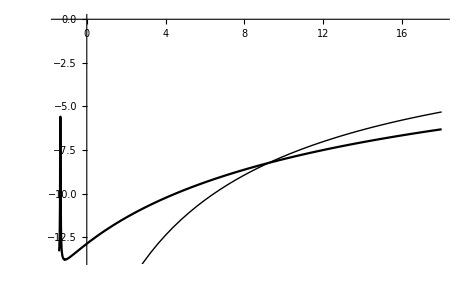

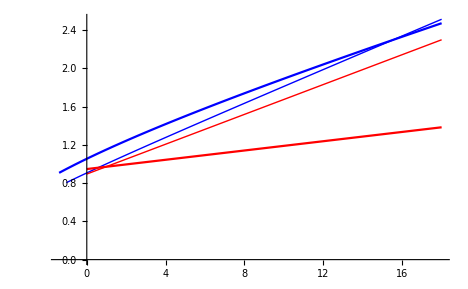

```mathematica
ClearAll["Global`*"];ParamsAreSet=False;
If[$VersionNumber<8,(*then*) Print["These programs require Mathematica version 8 or greater."];Abort[]];
If[Length[$FrontEnd] > 0,NBDir=SetDirectory[NotebookDirectory[]]];(* If running from the Notebook interface *)
rootDir = SetDirectory["../../.."];
AutoLoadDir=SetDirectory["./Mathematica/CoreCode/Autoload"];Get["./init.m"];
CoreCodeDir=SetDirectory[".."];
rootDir = SetDirectory[".."];
Get[CoreCodeDir<>"/MakeAnalyticalResults.m"];
Get[CoreCodeDir<>"/VarsAndFuncs.m"];
(* Method of creating figures depends on whether being run in batch mode or interactively *)
If[$FrontEnd == Null,OpenFigsUsingShell=True,OpenFigsUsingShell=False]; 
Get[CoreCodeDir<>"/ParametersBase.m"];
Severance=6;
𝒸Color=Blue;
𝓂DelEqZeroColor=Red;
𝓋Color=Black;
RHiThick=Thin;
RLowThick=Thick;
VerboseOutput=False;
PartCost=4;
mMaxPlotVal=18;
FindStableArm;
vERLoPlot=Plot[vE[𝓂]
,{𝓂,𝓂MinPermitted+PartCost,mMaxPlotVal}
,AxesOrigin->{0.,0.},PlotStyle->{𝓋Color,RLoThick}];
𝓂EDelEqZeroRLoPlot=Plot[𝓂EDelEqZero[𝓂]
,{𝓂,0,mMaxPlotVal}
,AxesOrigin->{0.,0.},PlotStyle->{𝓂DelEqZeroColor,RLoThick}];
cERLoPlot=Plot[cE[𝓂],
{𝓂,𝓂MinPermitted+PartCost,mMaxPlotVal}
,PlotRange->{Automatic,{0,cE[mMaxPlotVal]}},AxesOrigin->{0.,0.},PlotStyle->{𝒸Color,RLoThick}];
r=rBase+0.06;FindStableArm;
vERHiPlot=Plot[vE[𝓂-PartCost]
,{𝓂,𝓂MinPermitted+PartCost,mMaxPlotVal}
,AxesOrigin->{0.,0.},PlotStyle->{𝓋Color,RHiThick}];
Print[Show[vERLoPlot,vERHiPlot]];
cERHiPlot=Plot[cE[𝓂]
,{𝓂,𝓂MinPermitted+PartCost,mMaxPlotVal}
,PlotRange->{Automatic,{0,cE[mMaxPlotVal]}},AxesOrigin->{0.,0.},PlotStyle->{𝒸Color,RHiThick}];
𝓂EDelEqZeroRHiPlot=Plot[𝓂EDelEqZero[𝓂]
,{𝓂,0,mMaxPlotVal}
,AxesOrigin->{0.,0.},PlotStyle->{𝓂DelEqZeroColor,RHiThick}];
Print[Show[cERLoPlot,cERHiPlot,𝓂EDelEqZeroRLoPlot,𝓂EDelEqZeroRHiPlot
,PlotRange->{Automatic,{0,cE[mMaxPlotVal]}},AxesOrigin->{0.,0.}]];
```

```mathematica
??*DelEqZero*
```

```mathematica
𝒸EDelEqZero[1]
```

1.12292

```mathematica
PrecisionAugmentationFactor
```

1

```mathematica
(1+0.2)/(℧+0.2)
```

5.85366

```mathematica
℧
```

0.005

```mathematica
??𝓂EDelEqZero
```

Global`𝓂EDelEqZero

𝓂EDelEqZero[𝓂_]:=(Γ (1-SoiTax))/R+(1-Γ/R) 𝓂

2.

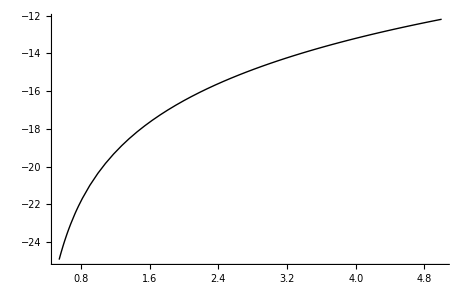

Solving ...

Below 𝓂MinPermitted after 81 backwards Euler iterations.

Last 2 Points:(0.738694 | 0.338181 | 0.37412 | -19.8354 | -0.241298
-0.0394911 | 0.210622 | -0.805623 | -19.0184 | -23.2462)

Solving ...

Above 𝓂MaxPermitted after 156 backwards Euler iterations.

Last 2 Points:(97.9516 | 8.09831 | 0.0704026 | -1.76886 | -0.0000154812
101.12 | 8.32131 | 0.0703555 | -1.72184 | -0.000014261)

```mathematica
ρ
```

```mathematica
Get[CoreCodeDir<>"/ParametersBase.m"];
{ r ,ϑ ,𝔤,℧}={rBase,ϑBase,𝔤Base,℧Base};
𝓂Max=1.5 𝓂E;
𝓂MaxMax=5 𝓂E;
FindStableArm;
κEBase = κE //N;𝒸EBase = 𝒸E //N;𝓂EOrig=𝓂EBase //N;

cFuncPlotBasePoints=Map[{{#,cE[#]}}&,Table[𝓂,{𝓂,0,𝓂MaxMax,0.01}]];
cFuncPlotBase=cFuncPlot=Plot[cE[𝓂],{𝓂,0,𝓂MaxMax}];
```

Solving ...

Below 𝓂MinPermitted after 49 backwards Euler iterations.

Last 2 Points:(0.963611 | 0.388829 | 0.308316 | -19.6594 | -0.176986
-0.00329179 | 0.0325698 | -9.23335 | -14.63 | -543.426)

Solving ...

Above 𝓂MaxPermitted after 95 backwards Euler iterations.

Last 2 Points:(96.7456 | 7.64463 | 0.0641646 | -2.10758 | -0.0000407635
102.363 | 8.00443 | 0.063948 | -2.01579 | -0.0000364637)

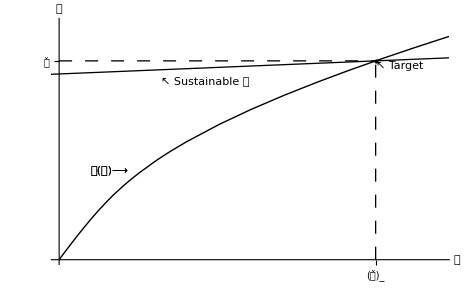

```mathematica
(* Now suppose that there is an exogenous perfectly certain increase to permanent income by the amount 0.2 per year - think of it as a government transfer received by everyone in the population (this is more transparent than introducing unemployment insurance *)
DebtLimPDV=0.2/((R)-𝔊);Stable𝓂LocusPlot=Plot[{𝓂EDelEqZero[𝓂]},{𝓂,-DebtLimPDV,𝓂MaxMax},PlotStyle->{Black,Thickness[0.002]}];
SimGeneratePath[𝓂E-2,30];
{𝓂MinNew,𝓂MaxNew}={0,20};
{𝒸MinNew,𝒸MaxNew}={0,2.};

Print[cFunc=Show[cFuncPlotBase,Stable𝓂LocusPlot
,Graphics[Text["↖ Sustainable 𝒸",{0.6 𝓂E,0.9 𝒸E},{1,0}]],Graphics[Text["𝒸(𝓂)⟶",{0.1 𝓂E,0.45 𝒸E},{-1,0}]]
,Graphics[{Thickness[0.002],Dashing[{0.02}],Line[{{𝓂E,0},{𝓂E,𝒸E}}]}]
,Graphics[{Thickness[0.002],Dashing[{0.02}],Line[{{0,𝒸E},{𝓂E,𝒸E}}]}]
,Graphics[Text[" ↖ Target",{𝓂E,𝒸E},{-1,1}]]
,Graphics[Text["𝒸(𝓂)⟶",{0.1 𝓂E,0.45 𝒸E},{-1,0}]]
,Graphics[{Black,PointSize[Medium],Point[{𝓂E,𝒸E}]}]
,Ticks->{{{𝓂E,"(𝓂̌)_"}},{{𝒸E,"𝒸̌"}}}
,PlotRange->{{𝓂MinNew,𝓂E+1},{𝒸MinNew,𝒸E+.2}}
,AxesLabel->{"𝓂","𝒸"}]];
```

```mathematica
ExportFigsToDir["cFunc",NBDir<>"/Figures"];
```

-Graphics-

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/Copenhagen/Figures/cFunc.xxx

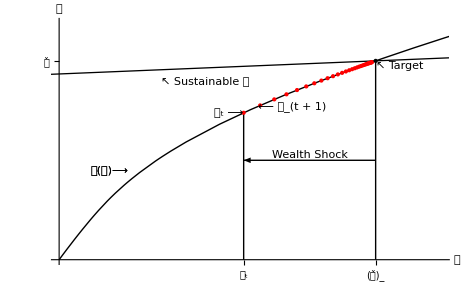

```mathematica
𝓂𝒸PathPlot = ListPlot[Take[𝓂𝒸Path,-(Length[𝓂𝒸Path]-1)],PlotStyle->{Red,PointSize[Medium]}];Print[WealthShock=Show[cFuncPlotBase,Stable𝓂LocusPlot,𝓂𝒸PathPlot,Graphics[Text["↖ Sustainable 𝒸",{0.6 𝓂E,0.9 𝒸E},{1,0}]]
,Graphics[Text["𝒸(𝓂)⟶",{0.1 𝓂E,0.45 𝒸E},{-1,0}]]
,Graphics[Line[{{𝓂E,0},{𝓂E,𝒸E}}]]
,Graphics[Line[{{𝓂E-2,0},{𝓂E-2,cE[𝓂E-2]}}]]
,Graphics[Arrow[{{𝓂E,𝒸E/2},{𝓂E-2,𝒸E/2}}]]
,Graphics[Text["𝒸_t ⟶",{𝓂E-2,cE[𝓂E-2]},{1,0}]]
,Graphics[Text[" ⟵ 𝒸_(t + 1)",{𝓂E-2+0.22,cE[𝓂E-2+0.22]},{-1,0}]]
,Graphics[Text["Wealth Shock",{𝓂E-1,𝒸E/2},{0,-1}]]
,Graphics[Text[" ↖ Target",{𝓂E,𝒸E},{-1,1}]]
,Graphics[Text["𝒸(𝓂)⟶",{0.1 𝓂E,0.45 𝒸E},{-1,0}]]
,Graphics[{Black,PointSize[Medium],Point[{𝓂E,𝒸E}]}]
,Ticks->{{{𝓂E,"(𝓂̌)_"},{𝓂E-2,"𝓂_t"}},{{𝒸E,"𝒸̌"}}}
,PlotRange->{{𝓂MinNew,𝓂E+1},{𝒸MinNew,𝒸E+.2}}
,AxesLabel->{"𝓂","𝒸"}]];
```

```mathematica
ExportFigsToDir["WealthShock",NBDir<>"/Figures"];
```

-Graphics-

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/Copenhagen/Figures/WealthShock.xxx

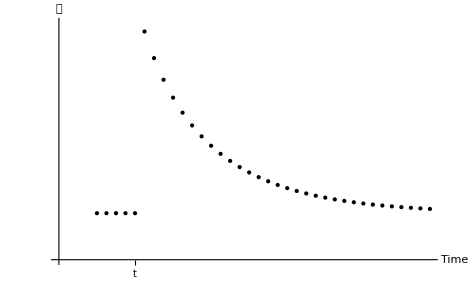

```mathematica
savRat=Flatten[Transpose[{1+((r)/R)(𝓂𝒸Path[[All,1]]-Table[1,{Length[𝓂𝒸Path]}])-𝓂𝒸Path[[All,2]]}]];
PrependTo[savRat,savRat[[1]]];
PrependTo[savRat,savRat[[1]]];
PrependTo[savRat,savRat[[1]]];
PrependTo[savRat,savRat[[1]]];
timePath=Table[i,{i,Length[savRat]}];
savPathPlot=ListPlot[Transpose[{timePath,savRat}],PlotRange->All,PlotStyle->{PointSize[Medium],Black}];
Print[savPathAfterWealthShock=Show[savPathPlot,Ticks->{{{5,"t"}},None},AxesLabel->{"Time","𝓈"},AxesOrigin->{-3,0},PlotRange->{{-3,Length[timePath]},{0.,Max[savRat]+0.01}}]];
```

```mathematica
ExportFigsToDir["savPathAfterWealthShock",NBDir<>"/Figures"];
```

-Graphics-

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/Copenhagen/Figures/savPathAfterWealthShock.xxx

```mathematica
Get[CoreCodeDir<>"/ParametersBase.m"];𝔤   =𝔤Base   =0.01;{𝒸EBase,𝓂EBase} = {𝒸E,𝓂E};

(* Restore the baseline parameter values and solve again *)
{ r ,ϑ ,𝔤,℧}={rBase,ϑBase,𝔤Base,3℧Base};
𝓂Max=1.5 𝓂E;
𝓂MaxMax=7 𝓂E;
FindStableArm;
κEBase = κE //N;𝒸EBase = 𝒸E //N;
cFuncPlotuHigher=Plot[cE[𝓂],{𝓂,0,𝓂MaxMax},PlotStyle->{Black,Thickness[0.002]}];

SimGeneratePath[𝓂EOrig,HowMany=15];


𝓂𝒸PathPlot = ListPlot[Take[𝓂𝒸Path,-(HowMany+1)],PlotStyle->{PointSize[Medium],Red}];


Get[CoreCodeDir<>"/ParametersBase.m"];𝔤   =𝔤Base   =0.01;{𝒸EBase,𝓂EBase} = {𝒸E,𝓂E};

(* Restore the baseline parameter values and solve again *)
{ r ,ϑ ,𝔤,℧}={rBase,ϑBase,𝔤Base,℧Base};
𝓂Max=1.5 𝓂E;
𝓂MaxMax=7 𝓂E;
FindStableArm;
κEBase = κE //N;𝒸EBase = 𝒸E //N;
```

Solving ...

Below 𝓂MinPermitted after 61 backwards Euler iterations.

Last 2 Points:(1.27706 | 0.348892 | 0.201263 | -25.9169 | -0.0780869
0.411009 | 0.135194 | 0.30358 | -43.1327 | -0.146735)

Solving ...

Above 𝓂MaxPermitted after 101 backwards Euler iterations.

Last 2 Points:(99.6974 | 7.50335 | 0.0639563 | -2.14727 | -0.0000348611
106.171 | 7.9167 | 0.0637437 | -2.03829 | -0.0000309102)

Solving ...

Below 𝓂MinPermitted after 49 backwards Euler iterations.

Last 2 Points:(0.963611 | 0.388829 | 0.308316 | -19.6594 | -0.176986
-0.00329179 | 0.0325698 | -9.23335 | -14.63 | -543.426)

Solving ...

Above 𝓂MaxPermitted after 95 backwards Euler iterations.

Last 2 Points:(96.7456 | 7.64463 | 0.0641646 | -2.10758 | -0.0000407635
102.363 | 8.00443 | 0.063948 | -2.01579 | -0.0000364637)

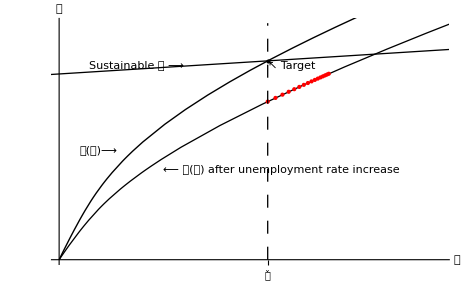

```mathematica
Print[cPhaseDiagBeforeAndAfteruRise=Show[cFuncPlotBase,cFuncPlotuHigher,Stable𝓂LocusPlot,𝓂𝒸PathPlot
,Graphics[Text["Sustainable 𝒸 ⟶",{0.6 𝓂E,0.98 𝒸E},{1,0}]]
,Graphics[Text["⟵ 𝒸(𝓂) after unemployment rate increase",{0.5 𝓂E,0.45 𝒸E},{-1,0}]]
,Graphics[{Thickness[0.002],Dashing[{0.02}],Line[{{𝓂E,0},{𝓂E,𝒸E+0.2}}]}]
,Graphics[Text[" ↖ Target",{𝓂E,𝒸E},{-1,1}]]
,Graphics[Text["𝒸(𝓂)⟶",{0.1 𝓂E,0.55 𝒸E},{-1,0}]]
,Graphics[{Black,PointSize[Medium],Point[{𝓂E,𝒸E}]}]
,Ticks->{{{𝓂E,"𝓂̌"}},None}
,PlotRange->{{𝓂MinNew,𝓂E+4},{𝒸MinNew,𝒸E+.2}}
,AxesLabel->{"𝓂","𝒸"}]];
```

```mathematica
ExportFigsToDir["cPhaseDiagBeforeAndAfteruRise",NBDir<>"/Figures"];
```

-Graphics-

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/Copenhagen/Figures/cPhaseDiagBeforeAndAfteruRise.xxx

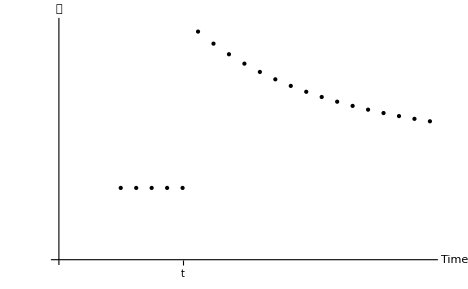

```mathematica
savAfteruRiseRat=Flatten[Transpose[{1+((r)/R)(𝓂𝒸Path[[All,1]]-Table[1,{Length[𝓂𝒸Path]}])-𝓂𝒸Path[[All,2]]}]];
PrependTo[savAfteruRiseRat,savAfteruRiseRat[[1]]];
PrependTo[savAfteruRiseRat,savAfteruRiseRat[[1]]];
PrependTo[savAfteruRiseRat,savAfteruRiseRat[[1]]];
PrependTo[savAfteruRiseRat,savAfteruRiseRat[[1]]];
timePath=Table[i,{i,Length[savAfteruRiseRat]}];
savAfteruRisePathPlot=ListPlot[Transpose[{timePath,savAfteruRiseRat}],PlotRange->All,PlotStyle->{PointSize[Medium],Black}];
Print[savAfteruRisePath=Show[savAfteruRisePathPlot,Ticks->{{{5,"t"}},None},AxesLabel->{"Time","𝓈"},AxesOrigin->{-3,0},PlotRange->{{-3,Length[timePath]},{0.,Max[savAfteruRiseRat]+0.01}}]];
```

```mathematica
ExportFigsToDir["savAfteruRisePath",NBDir<>"/Figures"];
```

-Graphics-

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/Copenhagen/Figures/savAfteruRisePath.xxx

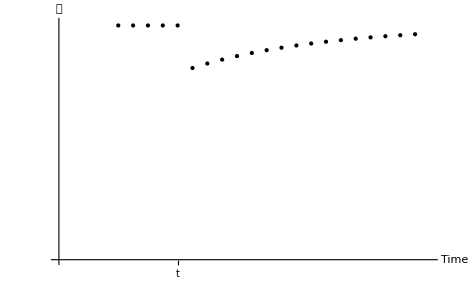

```mathematica
cRatAfteruRiseRat=𝓂𝒸Path[[All,2]];
Do[PrependTo[cRatAfteruRiseRat,cRatAfteruRiseRat[[1]]],{4}];
timePath=Table[i,{i,Length[cRatAfteruRiseRat]}];
cRatAfteruRisePathPlot=ListPlot[Transpose[{timePath,cRatAfteruRiseRat}],PlotRange->All,PlotStyle->{PointSize[Medium],Black}];
Print[cRatAfteruRisePath=Show[cRatAfteruRisePathPlot,Ticks->{{{5,"t"}},None},AxesLabel->{"Time","𝒸"},AxesOrigin->{-3,0},PlotRange->{{-3,Length[timePath]+1},{0.,Max[cRatAfteruRiseRat]+0.01}}]];
```

```mathematica
ExportFigsToDir["cRatAfteruRisePath",NBDir<>"/Figures"];
```

-Graphics-

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/Copenhagen/Figures/cRatAfteruRisePath.xxx

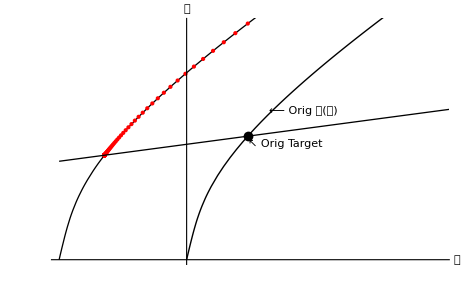

```mathematica
Clear[cE];
cE[m_]:= cEInterp[m+DebtLimPDV];

SimGeneratePath[𝓂E,100];
 cFuncPlotNew=Plot[cE[𝓂],{𝓂,-DebtLimPDV,𝓂MaxMax},PlotRange->All,PlotStyle->{Black,Thickness[0.002]}];
𝓂𝒸PathPlot = ListPlot[Take[𝓂𝒸Path,-(Length[𝓂𝒸Path]-1)],PlotStyle->{PointSize[Medium],Red}];
{𝓂MinNew,𝓂MaxNew}={0,20};
{𝒸MinNew,𝒸MaxNew}={0,2.};TractableBufferStockTarget=Show[cFuncPlotBase,Stable𝓂LocusPlot,Graphics[Text["Perm Inc ⟶",{0.6 𝓂E,0.98 𝒸E},{1,0}]],Graphics[Text["⟵ 𝒸(𝓂)",{0.9 𝓂E,0.85 𝒸E},{-1,0}]],Ticks->None
,PlotRange->{{𝓂MinNew,𝓂E+1},{𝒸MinNew,𝒸E+rBase+0.01}}
,AxesLabel->{"𝓂","𝒸"}];
Print[PhaseDiagramDebtLimRisePlot=Show[cFuncPlotNew,cFuncPlotBase,𝓂𝒸PathPlot,Stable𝓂LocusPlot
,Graphics[{PointSize[0.015],Point[{𝓂EBase,𝒸EBase}]}]
,Graphics[Text["↖ Orig Target ",{𝓂EBase,0.98 𝒸EBase},{-1,1}]],Graphics[Text[" ⟵ Orig 𝒸(𝓂) ",{1.35 𝓂EBase,1.2 𝒸EBase},{-1,0}]],Graphics[Text["  New 𝒸(𝓂) ⟶ ",{𝓂EBase+1,cE[𝓂EBase+1]},{1,0}]],Ticks->None,PlotRange->{{-DebtLimPDV,𝓂MaxNew},{𝒸MinNew,𝒸MaxNew+0.02}}
,AxesLabel->{"𝓂","𝒸"}]];
```

```mathematica
ExportFigsToDir["PhaseDiagramDebtLimRisePlot",NBDir<>"/Figures"];
Print[Show[PhaseDiagramDebtLimRisePlot]];
```

-Graphics-

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/Copenhagen/Figures/PhaseDiagramDebtLimRisePlot.xxx

-Graphics-

```mathematica
HowMany=75;
𝓂Path=Take[Transpose[𝓂𝒸Path]⟦1⟧,HowMany];
𝒸Path=Take[Transpose[𝓂𝒸Path]⟦2⟧,HowMany];
MPCPath=((cE[#1+10 ε]-cE[#1-10 ε])/(20 ε)&)/@Rest[𝓂Path];
PrependTo[𝓂Path,𝓂EBase];
PrependTo[𝒸Path,𝒸EBase];
PrependTo[MPCPath,κEBase];
PrependTo[𝓂Path,𝓂EBase];
PrependTo[𝒸Path,𝒸EBase];
PrependTo[MPCPath,κEBase];
PrependTo[𝓂Path,𝓂EBase];
PrependTo[𝒸Path,𝒸EBase];
PrependTo[MPCPath,κEBase];
PrependTo[MPCPath,κEBase];
timePath=Table[i,{i,Length[𝒸Path]}];
𝒸PathPlot=ListPlot[Transpose[{timePath,𝒸Path}],PlotRange->All];
𝓂PathPlot=ListPlot[Transpose[{timePath,𝓂Path}],PlotRange->All];
MPCPathPlot=ListPlot[Transpose[{timePath,MPCPath}],PlotRange->All];
```

```mathematica
cPathAfterDebtLimRise=Show[𝒸PathPlot,Ticks->{{{4,"0"}},None},AxesLabel->{"Time","𝒸"},AxesOrigin->{-3,0},PlotRange->{{-3,HowMany},{0.,Max[𝒸Path]+0.1}}];
mPathAfterDebtLimRise=Show[𝓂PathPlot,Graphics[{Dashing[{0.01}],Line[{{timePath⟦1⟧,𝓂EBase-DebtLimPDV-2.85},{timePath⟦-1⟧,𝓂EBase-DebtLimPDV-2.85}}]}],Graphics[Text["↑",{1/2 (timePath⟦1⟧+timePath⟦-1⟧),𝓂EBase-DebtLimPDV-0.55},{0,1}]],Graphics[Text["\!\(\*OverscriptBox[\(𝓂\), \(_\)]\)-d",{1/2 (timePath⟦1⟧+timePath⟦-1⟧),𝓂EBase-DebtLimPDV-0.85},{0,1}]],Ticks->{{{4,"0"}},None},AxesLabel->{"Time","𝓂"},AxesOrigin->{-3,0},PlotRange->{{-3,HowMany},{-DebtLimPDV,Max[𝓂Path]+1}}];
MPCPathAfterDebtLimRise=Show[MPCPathPlot,Graphics[{Dashing[{0.01}],Line[{{timePath⟦1⟧,κ},{timePath⟦-1⟧,κ}}]}],Graphics[Text["↑",{1/2 (timePath⟦1⟧+timePath⟦-1⟧),κ},{0,1}]],Graphics[Text["Perfect Foresight MPC",{1/2 (timePath⟦1⟧+timePath⟦-1⟧),(κ 4)/5},{0,1}]],Ticks->{{{4,"0"}},None},AxesLabel->{"Time","κ(𝓂)"},AxesOrigin->{-3,0},PlotRange->{{-3,HowMany},{0,0.15}}];
```

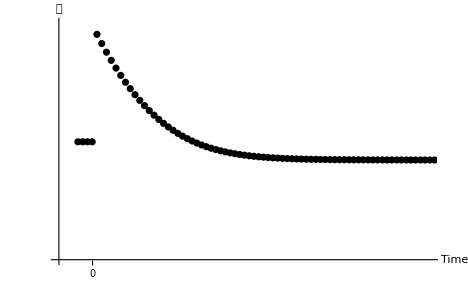

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/Copenhagen/Figures/cPathAfterDebtLimRise.xxx

```mathematica
ExportFigsToDir["cPathAfterDebtLimRise",NBDir<>"/Figures"];
```

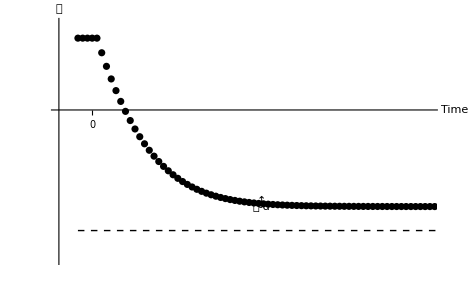

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/Copenhagen/Figures/mPathAfterDebtLimRise.xxx

```mathematica
ExportFigsToDir["mPathAfterDebtLimRise",NBDir<>"/Figures"];
```

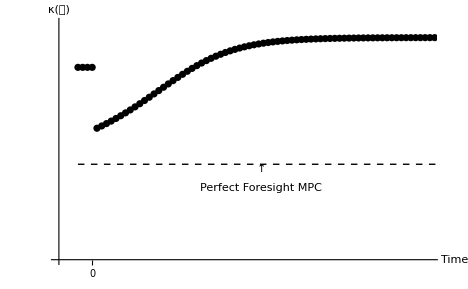

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/Copenhagen/Figures/MPCPathAfterDebtLimRise.xxx

```mathematica
ExportFigsToDir["MPCPathAfterDebtLimRise",NBDir<>"/Figures"];
```

```mathematica
savRat=Flatten[Transpose[{1+((r)/R)(𝓂𝒸Path[[All,1]]-Table[1,{Length[𝓂𝒸Path]}])-𝓂𝒸Path[[All,2]]}]];
PrependTo[savRat,savRat[[1]]];
PrependTo[savRat,savRat[[1]]];
PrependTo[savRat,savRat[[1]]];
PrependTo[savRat,savRat[[1]]];
timePath=Table[i,{i,Length[savRat]}];
savPathPlot=ListPlot[Take[Transpose[{timePath,savRat}],50],PlotRange->All,PlotStyle->{PointSize[Medium],Black}];
savPathAfterLiqConstrRelax=Show[savPathPlot,Ticks->{{{5,"t"}},None},AxesLabel->{"Time","𝓈"},AxesOrigin->{-3,Min[savRat]-0.02},PlotRange->{{-3,50},{Min[savRat]-0.02,Max[savRat]+0.01}}];
```

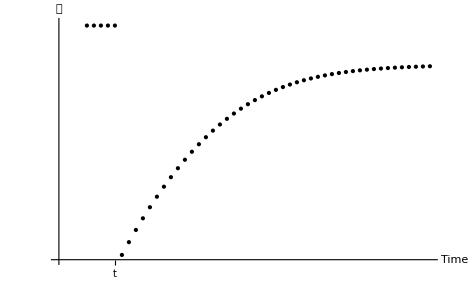

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/Copenhagen/Figures/savPathAfterLiqConstrRelax.xxx

```mathematica
ExportFigsToDir["savPathAfterLiqConstrRelax",NBDir<>"/Figures"];
```